```mathematica
Clear[ab,ηb]
```

```mathematica
a[η_?NumericQ] := ab*(1+(η/ηb)^2)^(1/2)
```

```mathematica
D[a[η], η]
```

(ab η)/(√(1+η^2/ηb^2) ηb^2)

```mathematica
Plot[m0*a[η], {η, -1, 1} ]
```

```mathematica
da[η_] := D[a[η], η]
NDSolve[{y'[η]==m0*da[η],y[ηi]==m0},y,{η,-ηi,ηi}]
```

NDSolve::mxst: Maximum number of 274526 steps reached at the point η == 9.87885×10^11.

{{y→                                  11         12
InterpolatingFunction[{{9.87885 10  , 2.96 10  }}, <>]}}

```mathematica
mb1 := m1* ab
Msol := 1989*10^(30) (*en gramos*)
m1 := 10^4*Msol
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

```mathematica
ax[x_] := ab*(1+x^2)^(1/2)
daxp[x_] := D[ax[x], x]
dax[x_?NumericQ]:=(ab x)/(√(1+x^2))
```

```mathematica
NDSolve[{y'[x]==m0*dax[x],y[xi]==m0},y,{x,-xi,xi}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[[x],{x,-10000,10000}]
```

-Graphics-

```mathematica
Plot[[x],{x,-xi,xi}]
```

-Graphics-

```mathematica
xinic := xi
```

```mathematica
s= NDSolve[{y'[x]==m0*dax[x],y[0]=="1.47384900000000000000000000000"×10^("29")},y,{x,-xinic,xinic},Method->"StiffnessSwitching", AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->30 ]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[y[x]/.s,{x,-xinic,-10^8}, PlotRange->All]
```

-Graphics-

```mathematica
Man[x_]:= mb1*(1+x^2)^(1/2)
Plot[Man[x], {x, -1000, 1000}]
```

-Graphics-

```mathematica
Man[0]
```

147384900000000000000000000000

```mathematica
ScientificForm[N[147384900000000000000000000000,30]]
```

1.47384900000000000000000000000×10^29

```mathematica
ScientificForm[N[147384900000000000000000000000,30]]
```

1.47384900000000000000000000000×10^29

```mathematica
Plot[{Man[x],y[x]/.s},{x,-xi,-10^7},PlotLegends->{"Analítica","Numérica"}]
```

-Graphics-

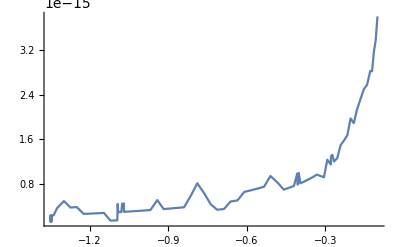

```mathematica
Plot[Abs[Man[x]-y[x]/.s]/Man[x],{x,-xi,-10^7},PlotRange->All]
```